```mathematica
SetDirectory[NotebookDirectory[]];
matchingStats=Import["../data/out/matching_stats.csv"];
```

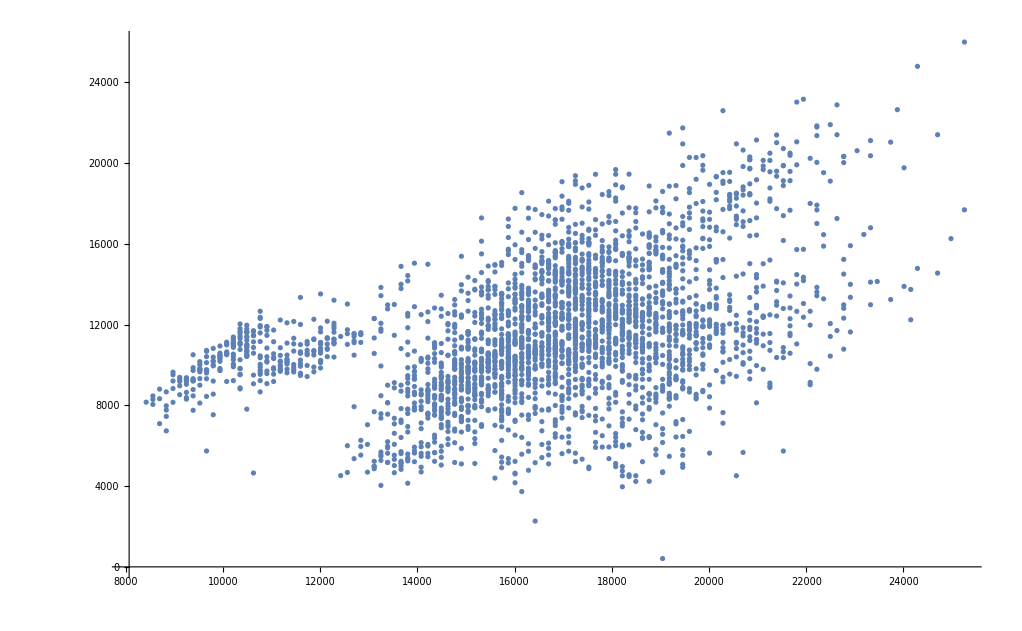

```mathematica
ListPlot[{#1*#2,#3}&@@@matchingStats]
```